# Single subband compact model

## parameter

### physical parameter

```mathematica
e=1.60218 10^-19;
kB=1.38066 10^-23;
h=6.62607 10^-34;
hbar=h/(2 π);
ϵ0=8.85418 10^-12;
T=300;
T1=325;
T2=350;
T3=375;
T4=400;
m0=9.10938 10^-31;
Nav=6.02214 10^23;
```

```mathematica
nm=10^-9;
um=10^-6;
cm=10^-2;
```

```mathematica
R=1nm;
Tox=0.5 nm;
```

```mathematica
ϵsi=11.9 ϵ0;
ϵox=3.9 ϵ0;
```

```mathematica
mt=0.19 m0;
ml=0.916 m0;
mr=2 (ml^-1+mt^-1)^-1;
```

```mathematica
mr/m0
```

0.31472

```mathematica
vt=(kB T)/e
```

0.0258522

```mathematica
vt1=(kB T1)/e
vt2=(kB T2)/e
vt3=(kB T3)/e
vt4=(kB T4)/e
```

0.0280065

0.0301608

0.0323152

0.0344695

```mathematica
wgc=0.;
wfb=0.;
```

```mathematica
Cox[r_,tox_]:=(2 π ϵox)/Log[1+tox/r]
```

### fermi-dirac integral function and its approximation

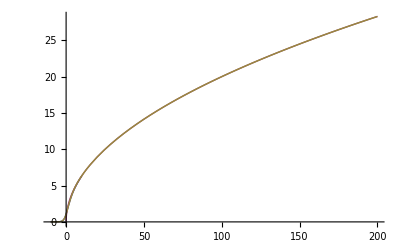

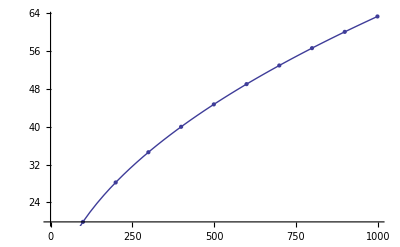

```mathematica
fermiintegral[j_,ζ_]:=-Gamma[1+j] PolyLog[1+j,-Exp[ζ]]
fermiinteralexpapp[j_,ξ_]:=Gamma[1+j] Exp[ξ]
fermiintegralappro[j_,ζ_]:=1/(j+1) ζ^(j+1)
fermiintegralaymerich[j_,ξ_]:=(((j+1) 2^(j+1))/(b+ξ+(Abs[ξ-b]^c+a^c)^(1/c))^(j+1)+Exp[-ξ]/Gamma[j+1])^-1/.a->(1+15/4 (j+1)+1/40 (j+1)^2)^(1/2)/.b->1.8+0.61 j/.c->2+(2-Sqrt[2]) 2^-j
Plot[{fermiintegral[-0.5,x],fermiintegralappro[-.5,x],fermiintegralaymerich[-.5,x]},{x,-10,200}]
Show[ListPlot[Table[{x,fermiintegralappro[-.5,x]},{x,-1,1000,100}]],Plot[fermiintegralaymerich[-.5,x],{x,-1,1000}]]
```

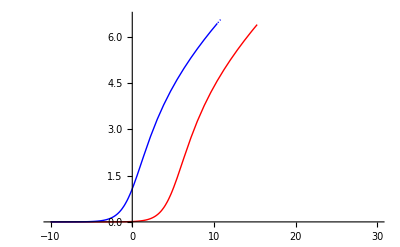

```mathematica
Plot[{fermiintegral[-.5,x-5],fermiintegral[-.5,x]},{x,-10,30},PlotStyle->{Red,Blue}]
```

```mathematica
besselenergylevel[nf_,nr_,m_,r_]:=hbar^2/(2 m) (BesselJZero[nf,nr]/r)^2(*represents the k^th zero of the Bessel function Subscript[J, n](x)*)
{{besselenergylevel[0,1,mr,R],besselenergylevel[0,1,mt,R],besselenergylevel[1,1,mr,R]}}//MatrixForm
```

(1.1217×10^-19 | 1.85801×10^-19 | 2.8477×10^-19)

```mathematica
Export["E:\\data_for_mathematica\\DeltaUgCalculation\\fermiintegral.txt",Table[{x,fermiintegralaymerich[-.5,x]},{x,-10,10,0.1}],"CSV"];
Export["E:\\data_for_mathematica\\DeltaUgCalculation\\fermiintegralseriesapprox.txt",Table[{x,fermiintegralappro[-.5,x]},{x,0,10,1}],"CSV"];
Export["E:\\data_for_mathematica\\DeltaUgCalculation\\fermiintegralexponantialapprox.txt",Table[{x,fermiinteralexpapp[-.5,x]},{x,-10,0,1}],"CSV"];
```

```mathematica
Exp[-10]
Sqrt[π]
```

1/ⅇ^10

√π

### Bessel function

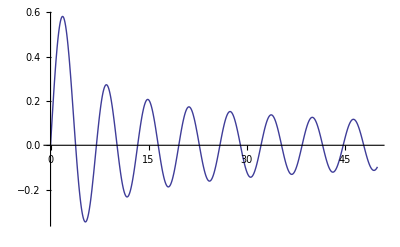

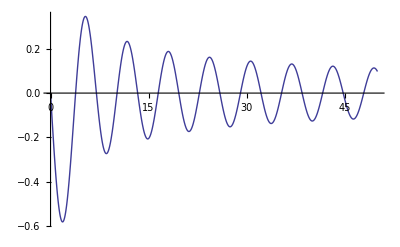

```mathematica
Plot[BesselJ[1,x],{x,0,50}]
Plot[BesselJ[-1,x],{x,0,50}]
```

```mathematica
besselelement[νf_,νr_,nf_,nr_]:=1/(2 Pi) Integrate[BesselJ[νf,BesselJZero[νf,νr] ζ]^2 ζ,{ζ,0,1}]^(-.5) Integrate[BesselJ[nf,BesselJZero[nf,nr] ζ]^2 ζ,{ζ,0,1}]^(-.5) Integrate[Exp[I (nf-νf) ϕ],{ϕ,0,2 Pi}] Integrate[BesselJ[νf,BesselJZero[νf,νr] ζ] (1-ζ^2) BesselJ[nf,BesselJZero[nf,nr] ζ] ζ,{ζ,0,1}]
```

```mathematica
valleykxky=4;
valleykz=2;
subbandtable={{valleykxky,mt/m0,besselenergylevel[0,1,mr,R]/e,besselenergylevel[0,1,mr,R]/(kB T),besselelement[0,1,0,1],0,besselenergylevel[0,1,mr,R]/e},{valleykz,ml/m0,besselenergylevel[0,1,mt,R]/e,besselenergylevel[0,1,mt,R]/(kB T),besselelement[0,1,0,1],0,besselenergylevel[0,1,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[1,1,mr,R]/e,besselenergylevel[1,1,mr,R]/(kB T),besselelement[1,1,1,1],0,besselenergylevel[1,1,mr,R]/e},{valleykz,ml/m0,besselenergylevel[1,1,mt,R]/e,besselenergylevel[1,1,mt,R]/(kB T),besselelement[1,1,1,1],0,besselenergylevel[1,1,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[0,2,mr,R]/e,besselenergylevel[0,2,mr,R]/(kB T),besselelement[0,2,0,2],0,besselenergylevel[0,2,mr,R]/e},{valleykz,ml/m0,besselenergylevel[0,2,mt,R]/e,besselenergylevel[0,2,mt,R]/(kB T),besselelement[0,2,0,2],0,besselenergylevel[0,2,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[1,2,mr,R]/e,besselenergylevel[1,2,mr,R]/(kB T),besselelement[1,2,1,2],0,besselenergylevel[1,2,mr,R]/e},{valleykz,ml/m0,besselenergylevel[1,2,mt,R]/e,besselenergylevel[1,2,mt,R]/(kB T),besselelement[1,2,1,2],0,besselenergylevel[0,2,mt,R]/e},{valleykxky,mt/m0,besselenergylevel[2,2,mr,R]/e,besselenergylevel[2,2,mr,R]/(kB T),besselelement[2,2,2,2],0,besselenergylevel[2,2,mr,R]/e},{valleykz,ml/m0,besselenergylevel[2,2,mt,R]/e,besselenergylevel[2,2,mt,R]/(kB T),besselelement[2,2,2,2],0,besselenergylevel[2,2,mt,R]/e}}(*gnv,mc,Eq0/e,Eq0/kBT,H0xx,reflection*)
```

{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}

## ΔUg numerical calculation

### lowest subband

#### defined parameter ΔUg

```mathematica
(*lowestsubbandug[vgs_,vds_,r_,tox_,st_]:=Re[FindRoot[4 Pi ϵsi U==e/(Pi hbar) Sqrt[(kB T mt)/2] st[[1,1]] (fermiintegral[-0.5,(vgs-wgc+wfb-(4 Pi ϵsi U)/Cox[r,tox])/vt-Eq01]+fermiintegral[-0.5,(vgs-wgc+wfb-(4 Pi ϵsi U)/Cox[r,tox])/vt-Eq01-vds/vt]) /.Eq01->st[[1,4]]+st[[1,5]] U/vt,{U,0.01}][[1,2]]]
Plot[lowestsubbandug[vgs,0.8,R,Tox,subbandtable],{vgs,-1,2}]*)
```

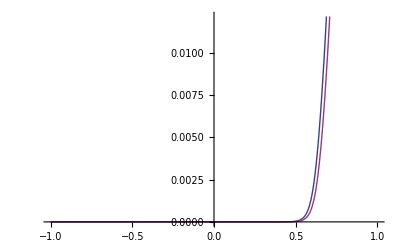

E:\data_for_mathematica\Deltaug\calculationfromfirstsubbandwithradius1nm.txt

```mathematica
lowestsubbandnumugamyrich[vgs_,vds_,r_,tox_,st_]:=Re[FindRoot[4 Pi ϵsi U==e/(Pi hbar) Sqrt[(kB T mt)/2] st[[1,1]] (fermiintegralaymerich[-0.5,(vgs-wgc+wfb-(4 Pi ϵsi U)/Cox[r,tox])/vt-Eq01]+fermiintegralaymerich[-0.5,(vgs-wgc+wfb-(4 Pi ϵsi U)/Cox[r,tox])/vt-Eq01-vds/vt]) /.Eq01->st[[1,4]]+st[[1,5]] U/vt,{U,0.01}][[1,2]]]
Plot[{lowestsubbandnumugamyrich[vgs,0,R,Tox,subbandtable],lowestsubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,1}]
Export["E:\data_for_mathematica\Deltaug\calculationfromfirstsubbandwithradius1nm.txt",Table[{vgs,lowestsubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,3,0.1}],"CSV"]
```

## numerical ID-VG characteristic

### lowest subband

FindRoot::nlnum: 在 {U} = {0.01} 处，函数值 {1.32405×10^-11 - 3.66231×10^-11\ (1/0.56419\ Power[« 2 »] + 0.707107\ Power[« 2 »] + 1/0.56419\ Power[« 2 »] + 0.707107\ Power[« 2 »])} 不是由数字组成的维度为 {1} 的列表.

General::stop: 在本次计算中，FindRoot :: nlnum 的进一步输出将被抑制.

Plot::exclul: {Im[ⅇ^-58.0265 + 38.6815\ (0.  + vgs + Times[« 2 »]) - 30.2467\ Re[Rule[« 2 »]]] - 0, Im[ⅇ^-27.0812 + 38.6815\ (0.  + vgs + Times[« 2 »]) - 30.2467\ Re[Rule[« 2 »]]] - 0} 必须是由方程或者实值函数组成的列表.

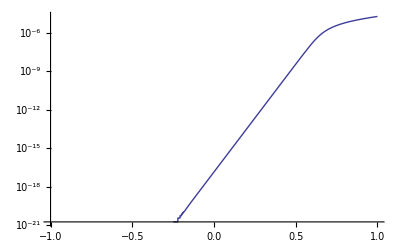

```mathematica
lowestsubbandnumids[vgs_,vds_,r_,tox_,st_]:=  (e kB T)/(Pi hbar) st[[1,1]] (Log[1+Exp[1/vt(vgs-wgc+wfb-(4 Pi ϵsi lowestsubbandnumugamyrich[vgs,vds,r,tox,st])/Cox[r,tox])-st[[1,4]]-st[[1,5]]/vt lowestsubbandnumugamyrich[vgs,vds,r,tox,st]]]-Log[1+Exp[1/vt(vgs-wgc+wfb-(4 Pi ϵsi lowestsubbandnumugamyrich[vgs,vds,r,tox,st])/Cox[r,tox])-st[[1,4]]-st[[1,5]]/vt lowestsubbandnumugamyrich[vgs,vds,r,tox,st]-vds/vt]])
LogPlot[lowestsubbandnumids[vgs,0.8,R,Tox,subbandtable],{vgs,-1,1}]
```

## ΔUg analytic calculation

### single band

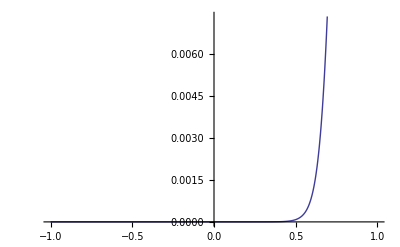

{{-1.,0.},{-0.95,0.},{-0.9,0.},{-0.85,0.},{-0.8,0.},{-0.75,0.},{-0.7,0.},{-0.65,0.},{-0.6,8.55916×10^-17},{-0.55,2.99571×10^-16},{-0.5,1.15549×10^-15},{-0.45,3.98001×10^-15},{-0.4,1.39514×10^-14},{-0.35,4.87444×10^-14},{-0.3,1.70113×10^-13},{-0.25,5.93835×10^-13},{-0.2,2.07264×10^-12},{-0.15,7.23429×10^-12},{-0.1,2.52502×10^-11},{-0.05,8.81318×10^-11},{0.,3.0761×10^-10},{0.05,1.07366×10^-9},{0.1,3.74746×10^-9},{0.15,1.30799×10^-8},{0.2,4.56533×10^-8},{0.25,1.59345×10^-7},{0.3,5.56159×10^-7},{0.35,1.94107×10^-6},{0.4,6.77358×10^-6},{0.45,0.0000236249},{0.5,0.0000822496},{0.55,0.000284568},{0.6,0.000964128},{0.65,0.00306289},{0.7,0.00831832},{0.75,0.0176182},{0.8,0.0294047},{0.85,0.0417873},{0.9,0.0539247},{0.95,0.0656002},{1.,0.0768004},{1.05,0.0875618},{1.1,0.0979272},{1.15,0.107936},{1.2,0.117623},{1.25,0.127016},{1.3,0.136141},{1.35,0.14502},{1.4,0.153671},{1.45,0.162111},{1.5,0.170356},{1.55,0.178417},{1.6,0.186306},{1.65,0.194035},{1.7,0.201612},{1.75,0.209047},{1.8,0.216346},{1.85,0.223518},{1.9,0.230568},{1.95,0.237502},{2.,0.244326},{2.05,0.251046},{2.1,0.257665},{2.15,0.264189},{2.2,0.27062},{2.25,0.276964},{2.3,0.283222},{2.35,0.2894},{2.4,0.2955},{2.45,0.301524},{2.5,0.307476},{2.55,0.313357},{2.6,0.319172},{2.65,0.32492},{2.7,0.330606},{2.75,0.336231},{2.8,0.341796},{2.85,0.347304},{2.9,0.352757},{2.95,0.358155},{3.,0.363501}}

E:\data_for_mathematica\Deltaug\calculationfromfirstsubwithradius1nm_a.txt

E:\data_for_mathematica\Deltaug\calculationfromfirstsubwithradius1nm_inversion.txt

E:\data_for_mathematica\Deltaug\calculationfromfirstsubwithradius1nm_subthresh.txt

```mathematica
allregionuga[vgs_] := 
 b/(2 a) (-1 + Sqrt[1 + (4 a)/(b b) 1/25 Log[1 + Exp[25 (vgs + c)]]]) /. 
    a -> (8 Pi^4 hbar^2 ϵsi^2)/(subbandtable[[1, 1]]^2 e^3 mt) /. 
   b -> subbandtable[[1, 5]] + (4 Pi ϵsi)/Cox[R, Tox] /. 
  c -> -wgc + wfb - subbandtable[[1, 3]]
inversion[vgs_]:= b/(2 a) (-1 + Sqrt[1 + (4 a)/(b b) (vgs + c)]) /. 
    a -> (8 Pi^4 hbar^2 ϵsi^2)/(subbandtable[[1, 1]]^2 e^3 mt) /. 
   b -> subbandtable[[1, 5]] + (4 Pi ϵsi)/Cox[R, Tox] /. 
  c -> -wgc + wfb - subbandtable[[1, 3]]
Plot[allregionuga[vgs], {vgs, -1, 1}]
Table[{vgs, allregionuga[vgs]}, {vgs, -1, 3, 0.05}]
Export["E:\data_for_mathematica\Deltaug\calculationfromfirstsubwithradius1nm_a.txt",Table[{vgs,allregionuga[vgs] },{vgs,-1,3,0.05}],"CSV"]
Export["E:\data_for_mathematica\Deltaug\calculationfromfirstsubwithradius1nm_inversion.txt",Table[{vgs, Re[inversion[vgs]]},{vgs,-1,3,0.05}],"CSV"]
Export["E:\data_for_mathematica\Deltaug\calculationfromfirstsubwithradius1nm_subthresh.txt",Table[{vgs, 0},{vgs,-1,0,0.05}],"CSV"]
```

```mathematica
(8 Pi^4 hbar^2 ϵsi^2)/(subbandtable[[1, 1]]^2 e^3 mt)
subbandtable[[1, 5]] + (4 Pi ϵsi)/Cox[R, Tox]
(4 Pi ϵsi)/Cox[R, Tox]
-wgc + wfb - subbandtable[[1, 3]]
```

8.44765

3.25632

2.47438

-0.700109

## analytic IDS-VGS characteristic

### lowest band

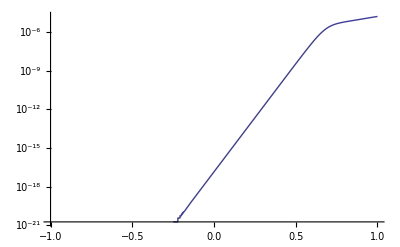

FindRoot::nlnum: 在 {U} = {0.01} 处，函数值 {1.32405×10^-11 - 3.66231×10^-11\ (1/0.56419\ Power[« 2 »] + 0.707107\ Power[« 2 »] + 1/0.56419\ Power[« 2 »] + 0.707107\ Power[« 2 »])} 不是由数字组成的维度为 {1} 的列表.

General::stop: 在本次计算中，FindRoot :: nlnum 的进一步输出将被抑制.

Plot::exclul: {Im[ⅇ^-58.0265 + 38.6815\ (0.  + vgs + Times[« 2 »]) - 30.2467\ Re[Rule[« 2 »]]] - 0, Im[ⅇ^-27.0812 + 38.6815\ (0.  + vgs + Times[« 2 »]) - 30.2467\ Re[Rule[« 2 »]]] - 0} 必须是由方程或者实值函数组成的列表.

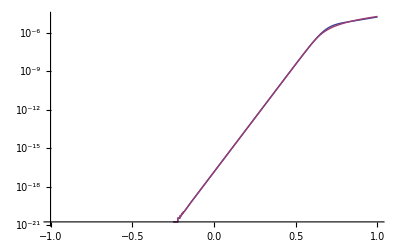

E:\data_for_mathematica\current\calculationofcurrentfromlowestsubbandwithradius1nm.txt

```mathematica
lowestsubbandanaids[vgs_,vds_,r_,tox_,st_]:=  (e kB T)/(Pi hbar) st[[1,1]] (Log[1+Exp[1/vt(vgs-wgc+wfb-(4 Pi ϵsi allregionuga[vgs])/Cox[r,tox])-st[[1,4]]-st[[1,5]]/vt allregionuga[vgs]]]-Log[1+Exp[1/vt(vgs-wgc+wfb-(4 Pi ϵsi allregionuga[vgs])/Cox[r,tox])-st[[1,4]]-st[[1,5]]/vt allregionuga[vgs]-vds/vt]])
LogPlot[{lowestsubbandanaids[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,1}]
LogPlot[{lowestsubbandanaids[vgs,0.8,R,Tox,subbandtable],lowestsubbandnumids[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,1}]
Export["E:\data_for_mathematica\current\calculationofcurrentfromlowestsubbandwithradius1nm.txt",Table[{vgs,lowestsubbandanaids[vgs, 0.8, R, Tox, subbandtable]},{vgs,-1,3,0.01}],"CSV"]
```

```mathematica
"E:\\data_for_mathematica\\current\\calculationofcurrentfromlowestsubbandwithradius3nm.txt"
```

E:\data_for_mathematica\current\calculationofcurrentfromlowestsubbandwithradius3nm.txt

## analytic IDS-VDS characteristic

```mathematica
Plot[{idswithtwobandsana[0.5,vds],towsubbandsnumids[0.5,vds,R,Tox,subbandtable]},{vds,0,1}]
Plot[{idswithtwobandsana[0.75,vds],towsubbandsnumids[0.75,vds,R,Tox,subbandtable]},{vds,0,1}]
Plot[{idswithtwobandsana[1,vds],towsubbandsnumids[1,vds,R,Tox,subbandtable]},{vds,0,1}]
Column[Table[{vgs,towsubbandsnumids[vgs,0.8,R,Tox,subbandtable]},{vgs,-0.95,1.05,0.05}]];
Column[Table[{vgs,idswithtwobandsana[vgs,0.8]},{vgs,0,1,0.05}]];
Column[Table[{vds,idswithtwobandsana[0.5,vds],towsubbandsnumids[0.5,vds,R,Tox,subbandtable],idswithtwobandsana[0.75,vds],towsubbandsnumids[0.75,vds,R,Tox,subbandtable],idswithtwobandsana[1,vds],towsubbandsnumids[1,vds,R,Tox,subbandtable]},{vds,0,1,0.01}],"CSV"]
```

-Graphics-

-Graphics-

-Graphics-

«1»

```mathematica
subbandtable[[1,5]]
```

0.781943

```mathematica
subbandtable[[2,4]]+(subbandtable[[2,5]] u)/vt
```

44.8579+30.2467 u

```mathematica
subbandtable[[2,3]]
```

1.15967

```mathematica
subbandtable
```

{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}

```mathematica
e kB T/(Pi hbar)
```

2.00306×10^-6

## energy calculation

```mathematica
Eq01single[vgs_]:=-ws+(subbandtable[[1,3]]+subbandtable[[1,5]] allregionuga[vgs])/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] allregionuga[vgs]
Eq01Hduble[vgs_,vds_,r_,tox_,subta_]:=-ws+(subbandtable[[1,3]]+(subbandtable[[1,5]] analytictwoSubbandunified[vgs,vds,R,Tox,subbandtable]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] analytictwoSubbandunified[vgs,vds,R,Tox,subbandtable]
Eq01Ldouble[vgs_,vds_,r_,tox_,subta_]:=-ws+(subbandtable[[2,3]]+(subbandtable[[2,5]] analytictwoSubbandunified[vgs,vds,R,Tox,subbandtable]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] analytictwoSubbandunified[vgs,vds,R,Tox,subbandtable]
NSeq01single[vgs_,vds_,r_,tox_,subta_]:=-ws+(subbandtable[[1,3]]+(subbandtable[[1,5]]lowestsubbandnumugamyrich[vgs,vds,R,Tox,subbandtable]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] lowestsubbandnumugamyrich[vgs,vds,R,Tox,subbandtable]
NSeq01H[vgs_,vds_,r_,tox_,subta_]:=-ws+(subbandtable[[1,3]]+(subbandtable[[1,5]]twosubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] twosubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable]
NSeq01L[vgs_,vds_,r_,tox_,subta_]:=-ws+(subbandtable[[2,3]]+(subbandtable[[2,5]] twosubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] twosubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable]
```

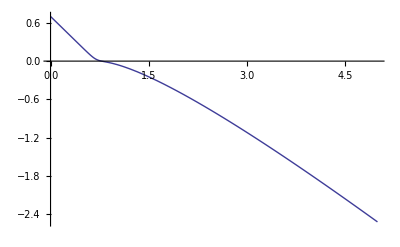

{-1.,1.70011,1.70011+3.25632 analytictwoSubbandunified[-1.,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],2.15967+3.25632 analytictwoSubbandunified[-1.,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{-0.95,1.65011,1.65011+3.25632 analytictwoSubbandunified[-0.95,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],2.10967+3.25632 analytictwoSubbandunified[-0.95,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{-0.9,1.60011,1.60011+3.25632 analytictwoSubbandunified[-0.9,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],2.05967+3.25632 analytictwoSubbandunified[-0.9,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{-0.85,1.55011,1.55011+3.25632 analytictwoSubbandunified[-0.85,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],2.00967+3.25632 analytictwoSubbandunified[-0.85,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{-0.8,1.50011,1.50011+3.25632 analytictwoSubbandunified[-0.8,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],1.95967+3.25632 analytictwoSubbandunified[-0.8,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{-0.75,1.45011,1.45011+3.25632 analytictwoSubbandunified[-0.75,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],1.90967+3.25632 analytictwoSubbandunified[-0.75,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{-0.7,1.40011,1.40011+3.25632 analytictwoSubbandunified[-0.7,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],1.85967+3.25632 analytictwoSubbandunified[-0.7,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{-0.65,1.35011,1.35011+3.25632 analytictwoSubbandunified[-0.65,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],1.80967+3.25632 analytictwoSubbandunified[-0.65,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{-0.6,1.30011,1.30011+3.25632 analytictwoSubbandunified[-0.6,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],1.75967+3.25632 analytictwoSubbandunified[-0.6,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{-0.55,1.25011,1.25011+3.25632 analytictwoSubbandunified[-0.55,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],1.70967+3.25632 analytictwoSubbandunified[-0.55,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{-0.5,1.20011,1.20011+3.25632 analytictwoSubbandunified[-0.5,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],1.65967+3.25632 analytictwoSubbandunified[-0.5,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{-0.45,1.15011,1.15011+3.25632 analytictwoSubbandunified[-0.45,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],1.60967+3.25632 analytictwoSubbandunified[-0.45,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{-0.4,1.10011,1.10011+3.25632 analytictwoSubbandunified[-0.4,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],1.55967+3.25632 analytictwoSubbandunified[-0.4,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{-0.35,1.05011,1.05011+3.25632 analytictwoSubbandunified[-0.35,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],1.50967+3.25632 analytictwoSubbandunified[-0.35,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{-0.3,1.00011,1.00011+3.25632 analytictwoSubbandunified[-0.3,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],1.45967+3.25632 analytictwoSubbandunified[-0.3,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{-0.25,0.950109,0.950109+3.25632 analytictwoSubbandunified[-0.25,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],1.40967+3.25632 analytictwoSubbandunified[-0.25,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{-0.2,0.900109,0.900109+3.25632 analytictwoSubbandunified[-0.2,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],1.35967+3.25632 analytictwoSubbandunified[-0.2,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{-0.15,0.850109,0.850109+3.25632 analytictwoSubbandunified[-0.15,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],1.30967+3.25632 analytictwoSubbandunified[-0.15,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{-0.1,0.800109,0.800109+3.25632 analytictwoSubbandunified[-0.1,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],1.25967+3.25632 analytictwoSubbandunified[-0.1,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{-0.05,0.750109,0.750109+3.25632 analytictwoSubbandunified[-0.05,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],1.20967+3.25632 analytictwoSubbandunified[-0.05,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{0.,0.700109,0.700109+3.25632 analytictwoSubbandunified[0.,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],1.15967+3.25632 analytictwoSubbandunified[0.,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{0.05,0.650109,0.650109+3.25632 analytictwoSubbandunified[0.05,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],1.10967+3.25632 analytictwoSubbandunified[0.05,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{0.1,0.600109,0.600109+3.25632 analytictwoSubbandunified[0.1,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],1.05967+3.25632 analytictwoSubbandunified[0.1,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{0.15,0.550109,0.550109+3.25632 analytictwoSubbandunified[0.15,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],1.00967+3.25632 analytictwoSubbandunified[0.15,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{0.2,0.500109,0.500109+3.25632 analytictwoSubbandunified[0.2,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],0.959674+3.25632 analytictwoSubbandunified[0.2,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{0.25,0.450109,0.450109+3.25632 analytictwoSubbandunified[0.25,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],0.909674+3.25632 analytictwoSubbandunified[0.25,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{0.3,0.40011,0.400109+3.25632 analytictwoSubbandunified[0.3,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],0.859674+3.25632 analytictwoSubbandunified[0.3,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{0.35,0.350115,0.350109+3.25632 analytictwoSubbandunified[0.35,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],0.809674+3.25632 analytictwoSubbandunified[0.35,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{0.4,0.300131,0.300109+3.25632 analytictwoSubbandunified[0.4,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],0.759674+3.25632 analytictwoSubbandunified[0.4,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{0.45,0.250186,0.250109+3.25632 analytictwoSubbandunified[0.45,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],0.709674+3.25632 analytictwoSubbandunified[0.45,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{0.5,0.200376,0.200109+3.25632 analytictwoSubbandunified[0.5,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],0.659674+3.25632 analytictwoSubbandunified[0.5,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{0.55,0.151035,0.150109+3.25632 analytictwoSubbandunified[0.55,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],0.609674+3.25632 analytictwoSubbandunified[0.55,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{0.6,0.103248,0.100109+3.25632 analytictwoSubbandunified[0.6,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],0.559674+3.25632 analytictwoSubbandunified[0.6,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{0.65,0.0600823,0.0501086+3.25632 analytictwoSubbandunified[0.65,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],0.509674+3.25632 analytictwoSubbandunified[0.65,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{0.7,0.0271957,0.000108573+3.25632 analytictwoSubbandunified[0.7,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],0.459674+3.25632 analytictwoSubbandunified[0.7,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{0.75,0.0074792,-0.0498914+3.25632 analytictwoSubbandunified[0.75,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],0.409674+3.25632 analytictwoSubbandunified[0.75,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{0.8,-0.00414031,-0.0998914+3.25632 analytictwoSubbandunified[0.8,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],0.359674+3.25632 analytictwoSubbandunified[0.8,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{0.85,-0.0138188,-0.149891+3.25632 analytictwoSubbandunified[0.85,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],0.309674+3.25632 analytictwoSubbandunified[0.85,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{0.9,-0.0242954,-0.199891+3.25632 analytictwoSubbandunified[0.9,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],0.259674+3.25632 analytictwoSubbandunified[0.9,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{0.95,-0.0362762,-0.249891+3.25632 analytictwoSubbandunified[0.95,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],0.209674+3.25632 analytictwoSubbandunified[0.95,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}
{1.,-0.0498047,-0.299891+3.25632 analytictwoSubbandunified[1.,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}],0.159674+3.25632 analytictwoSubbandunified[1.,0.8,1/1000000000,5.×10^-10,{{4,0.19,0.700109,27.0812,0.781943,0,0.700109},{2,0.916,1.15967,44.8579,0.781943,0,1.15967},{4,0.19,1.77739,68.7521,0.666667,0,1.77739},{2,0.916,2.9441,113.882,0.666667,0,2.9441},{4,0.19,3.68883,142.689,0.688545,0,3.68883},{2,0.916,6.11025,236.354,0.688545,0,6.11025},{4,0.19,5.95835,230.478,0.666667,0,5.95835},{2,0.916,9.86953,381.768,0.666667,0,6.11025},{4,0.19,8.57705,331.773,0.638438,0,8.57705},{2,0.916,14.2072,549.556,0.638438,0,14.2072}}]}

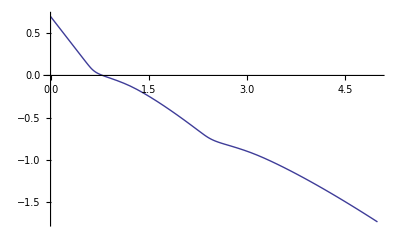

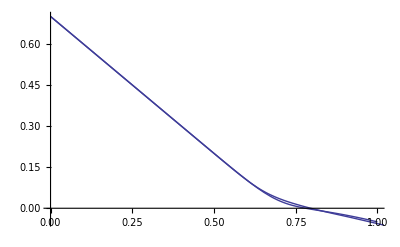

«1»

E:\data_for_mathematica\R2nmEnergyCalculation\NumericalEnergyLevelsingleband.txt

E:\data_for_mathematica\R2nmEnergyCalculation\NumericalEnergyLevelHighersubband.txt

E:\data_for_mathematica\R2nmEnergyCalculation\NumericalEnergyLevelLowersubband.txt

E:\data_for_mathematica\R2nmEnergyCalculation\analyticEnergyLevelLowersubband.txt

E:\data_for_mathematica\R2nmEnergyCalculation\analyticEnergyLevelHighersubband.txt

```mathematica
Plot[{Eq01single[vgs],Eq01Hduble[vgs,0.8,R,Tox,subbandtable],Eq01Ldouble[vgs,0.8,R,Tox,subbandtable]},{vgs,0,5}]
Column[Table[{vgs,Eq01single[vgs],Eq01Hduble[vgs,0.8,R,Tox,subbandtable],Eq01Ldouble[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,1,0.05}]]
Plot[{NSeq01single[vgs,0.8,R,Tox,subbandtable],NSeq01H[vgs,0.8,R,Tox,subbandtable],NSeq01L[vgs,0.8,R,Tox,subbandtable]},{vgs,0,5}]
Show[Plot[{Eq01single[vgs],Eq01Hduble[vgs,0.8,R,Tox,subbandtable],Eq01Ldouble[vgs,0.8,R,Tox,subbandtable]},{vgs,0,1}],Plot[{NSeq01single[vgs,0.8,R,Tox,subbandtable],NSeq01H[vgs,0.8,R,Tox,subbandtable],NSeq01L[vgs,0.8,R,Tox,subbandtable]},{vgs,0,5}]]
Column[Table[{vgs,NSeq01single[vgs,0.8,R,Tox,subbandtable],NSeq01H[vgs,0.8,R,Tox,subbandtable],NSeq01L[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,5,0.05}]]
Export["E:\data_for_mathematica\R2nmEnergyCalculation\NumericalEnergyLevelsingleband.txt",Table[{vgs,NSeq01single[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,5,0.05}]]
Export["E:\data_for_mathematica\R2nmEnergyCalculation\NumericalEnergyLevelHighersubband.txt",Table[{vgs,NSeq01H[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,5,0.01}]]
Export["E:\data_for_mathematica\R2nmEnergyCalculation\NumericalEnergyLevelLowersubband.txt",Table[{vgs,NSeq01L[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,5,0.01}]]
Export["E:\data_for_mathematica\R2nmEnergyCalculation\analyticEnergyLevelLowersubband.txt",Table[{vgs,Eq01Ldouble[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,5,0.1}]]
Export["E:\data_for_mathematica\R2nmEnergyCalculation\analyticEnergyLevelHighersubband.txt",Table[{vgs,Eq01Hduble[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,5,0.1}]]
```

## multisubband calculation

Plot::exclul: {Im[Abs[-59.5215 - 30.2467\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, (38.6815\ Im[-2.47438\ U + vgs] + Im[-30.2467\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0, Im[Abs[-28.5762 - 30.2467\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, (38.6815\ Im[-2.47438\ U + vgs] + Im[-30.2467\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0} 必须是由方程或者实值函数组成的列表.

Plot::exclul: {Im[Abs[-77.2981 - 30.2467\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, (38.6815\ Im[-2.47438\ U + vgs] + Im[-30.2467\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0, Im[Abs[-46.3529 - 30.2467\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, « 6 », (38.6815\ Im[-2.47438\ U + vgs] + Im[-25.7877\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0, Im[Abs[-70.2471 - 25.7877\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, (38.6815\ Im[-2.47438\ U + vgs] + Im[-25.7877\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0} 必须是由方程或者实值函数组成的列表.

Plot::exclul: {Im[Abs[-77.2981 - 30.2467\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, (38.6815\ Im[-2.47438\ U + vgs] + Im[-30.2467\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0, Im[Abs[-46.3529 - 30.2467\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, « 14 », (38.6815\ Im[-2.47438\ U + vgs] + Im[-25.7877\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0, Im[Abs[-70.2471 - 25.7877\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, (38.6815\ Im[-2.47438\ U + vgs] + Im[-25.7877\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0} 必须是由方程或者实值函数组成的列表.

General::stop: 在本次计算中，Plot :: exclul 的进一步输出将被抑制.

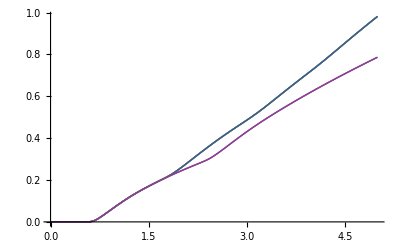

{-1.,0.,0.,0.,0.,0.,0.}
{-0.95,2.52435×10^-29,2.52435×10^-29,2.52435×10^-29,2.52435×10^-29,2.52435×10^-29,2.52435×10^-29}
{-0.9,7.57306×10^-29,7.57306×10^-29,7.57306×10^-29,7.57306×10^-29,7.57306×10^-29,7.57306×10^-29}
{-0.85,4.41762×10^-28,4.41762×10^-28,4.41762×10^-28,4.41762×10^-28,4.41762×10^-28,4.41762×10^-28}
{-0.8,3.09233×10^-27,3.09233×10^-27,3.09233×10^-27,3.09233×10^-27,3.09233×10^-27,3.09233×10^-27}
{-0.75,2.13813×10^-26,2.13813×10^-26,2.13813×10^-26,2.13813×10^-26,2.13813×10^-26,2.13813×10^-26}
{-0.7,1.47839×10^-25,1.47839×10^-25,1.47839×10^-25,1.47839×10^-25,1.47839×10^-25,1.47839×10^-25}
{-0.65,1.02267×10^-24,1.02267×10^-24,1.02267×10^-24,1.02267×10^-24,1.02267×10^-24,1.02267×10^-24}
{-0.6,7.07443×10^-24,7.07443×10^-24,7.07443×10^-24,7.07443×10^-24,7.07443×10^-24,7.07443×10^-24}
{-0.55,4.89383×10^-23,4.89383×10^-23,4.89383×10^-23,4.89383×10^-23,4.89383×10^-23,4.89383×10^-23}
{-0.5,3.38538×10^-22,3.38538×10^-22,3.38538×10^-22,3.38538×10^-22,3.38538×10^-22,3.38538×10^-22}
{-0.45,2.34188×10^-21,2.34188×10^-21,2.34188×10^-21,2.34188×10^-21,2.34188×10^-21,2.34188×10^-21}
{-0.4,1.62003×10^-20,1.62003×10^-20,1.62003×10^-20,1.62003×10^-20,1.62003×10^-20,1.62003×10^-20}
{-0.35,1.12068×10^-19,1.12068×10^-19,1.12068×10^-19,1.12068×10^-19,1.12068×10^-19,1.12068×10^-19}
{-0.3,7.75245×10^-19,7.75245×10^-19,7.75245×10^-19,7.75245×10^-19,7.75245×10^-19,7.75245×10^-19}
{-0.25,5.36287×10^-18,5.36287×10^-18,5.36287×10^-18,5.36287×10^-18,5.36287×10^-18,5.36287×10^-18}
{-0.2,3.70984×10^-17,3.70984×10^-17,3.70984×10^-17,3.70984×10^-17,3.70984×10^-17,3.70984×10^-17}
{-0.15,2.56634×10^-16,2.56634×10^-16,2.56634×10^-16,2.56634×10^-16,2.56634×10^-16,2.56634×10^-16}
{-0.1,1.7753×10^-15,1.7753×10^-15,1.7753×10^-15,1.7753×10^-15,1.7753×10^-15,1.7753×10^-15}
{-0.05,1.22809×10^-14,1.22809×10^-14,1.22809×10^-14,1.22809×10^-14,1.22809×10^-14,1.22809×10^-14}
{0.,8.49548×10^-14,8.49548×10^-14,8.49548×10^-14,8.49548×10^-14,8.49548×10^-14,8.49548×10^-14}
{0.05,5.87687×10^-13,5.87687×10^-13,5.87687×10^-13,5.87687×10^-13,5.87687×10^-13,5.87687×10^-13}
{0.1,4.06541×10^-12,4.06541×10^-12,4.06541×10^-12,4.06541×10^-12,4.06541×10^-12,4.06541×10^-12}
{0.15,2.8123×10^-11,2.8123×10^-11,2.8123×10^-11,2.8123×10^-11,2.8123×10^-11,2.8123×10^-11}
{0.2,1.94545×10^-10,1.94545×10^-10,1.94545×10^-10,1.94545×10^-10,1.94545×10^-10,1.94545×10^-10}
{0.25,1.34579×10^-9,1.34579×10^-9,1.34579×10^-9,1.34579×10^-9,1.34579×10^-9,1.34579×10^-9}
{0.3,9.3097×10^-9,9.30971×10^-9,9.30971×10^-9,9.30971×10^-9,9.30971×10^-9,9.3097×10^-9}
{0.35,6.44007×10^-8,6.44007×10^-8,6.44007×10^-8,6.44007×10^-8,6.44007×10^-8,6.44007×10^-8}
{0.4,4.45477×10^-7,4.45477×10^-7,4.45477×10^-7,4.45477×10^-7,4.45477×10^-7,4.45477×10^-7}
{0.45,3.08051×10^-6,3.08051×10^-6,3.08051×10^-6,3.08051×10^-6,3.08051×10^-6,3.08051×10^-6}
{0.5,0.0000212554,0.0000212554,0.0000212554,0.0000212554,0.0000212554,0.0000212554}
{0.55,0.00014451,0.00014451,0.00014451,0.00014451,0.00014451,0.00014451}
{0.6,0.000899005,0.000899005,0.000899005,0.000899005,0.000899005,0.000899005}
{0.65,0.00401089,0.00401089,0.00401089,0.00401089,0.00401089,0.00401089}
{0.7,0.0107186,0.0107186,0.0107186,0.0107186,0.0107186,0.0107186}
{0.75,0.0198956,0.0198956,0.0198956,0.0198956,0.0198956,0.0198956}
{0.8,0.0303018,0.0303018,0.0303018,0.0303018,0.0303018,0.0303018}
{0.85,0.0412997,0.0412997,0.0412997,0.0412997,0.0412997,0.0412997}
{0.9,0.0525639,0.0525639,0.0525639,0.0525639,0.0525639,0.0525639}
{0.95,0.0638405,0.0638405,0.0638405,0.0638405,0.0638405,0.0638405}
{1.,0.0749197,0.0749197,0.0749197,0.0749197,0.0749197,0.0749197}
{1.05,0.0858006,0.0858006,0.0858006,0.0858006,0.0858006,0.0858006}
{1.1,0.0964909,0.0964909,0.0964909,0.0964909,0.0964909,0.0964909}
{1.15,0.106915,0.106915,0.106915,0.106915,0.106915,0.106915}
{1.2,0.11699,0.11699,0.11699,0.11699,0.11699,0.11699}
{1.25,0.126681,0.126681,0.126681,0.126681,0.126681,0.126681}
{1.3,0.136002,0.136002,0.136002,0.136002,0.136002,0.136002}
{1.35,0.144992,0.144992,0.144992,0.144992,0.144992,0.144992}
{1.4,0.153698,0.153699,0.153699,0.153699,0.153699,0.153698}
{1.45,0.16216,0.162162,0.162162,0.162162,0.162162,0.16216}
{1.5,0.170408,0.170415,0.170415,0.170415,0.170415,0.170408}
{1.55,0.178467,0.178483,0.178483,0.178483,0.178483,0.178467}
{1.6,0.186351,0.186393,0.186393,0.186393,0.186393,0.186351}
{1.65,0.194074,0.194184,0.194184,0.194184,0.194184,0.194074}
{1.7,0.201645,0.201938,0.201938,0.201938,0.201938,0.201645}
{1.75,0.209075,0.209829,0.209829,0.209829,0.209829,0.209075}
{1.8,0.216371,0.218173,0.218173,0.218173,0.218173,0.216371}
{1.85,0.223539,0.227328,0.227328,0.227328,0.227328,0.223539}
{1.9,0.230586,0.237432,0.237432,0.237432,0.237432,0.230586}
{1.95,0.237518,0.248342,0.248342,0.248342,0.248342,0.237518}
{2.,0.244341,0.259818,0.259818,0.259818,0.259818,0.244341}
{2.05,0.251059,0.271655,0.271655,0.271655,0.271655,0.251059}
{2.1,0.257679,0.283712,0.283712,0.283712,0.283712,0.257679}
{2.15,0.264207,0.295888,0.295888,0.295888,0.295888,0.264207}
{2.2,0.270655,0.308085,0.308085,0.308085,0.308085,0.270655}
{2.25,0.277051,0.320197,0.320197,0.320197,0.320197,0.277051}
{2.3,0.283477,0.33219,0.33219,0.33219,0.33219,0.283477}
{2.35,0.290142,0.344081,0.344081,0.344081,0.344081,0.290142}
{2.4,0.297479,0.355872,0.355872,0.355872,0.355872,0.297479}
{2.45,0.305965,0.367537,0.367537,0.367537,0.367537,0.305965}
{2.5,0.315688,0.379041,0.379041,0.379041,0.379041,0.315688}
{2.55,0.326354,0.390361,0.390361,0.390361,0.390361,0.326354}
{2.6,0.337619,0.401491,0.401491,0.401491,0.401491,0.337619}
{2.65,0.349237,0.412437,0.412437,0.412437,0.412437,0.349237}
{2.7,0.361048,0.423215,0.423215,0.423215,0.423215,0.361048}
{2.75,0.37292,0.433844,0.433844,0.433844,0.433844,0.37292}
{2.8,0.38471,0.444346,0.444346,0.444346,0.444346,0.38471}
{2.85,0.396359,0.454747,0.454747,0.454747,0.454747,0.396359}
{2.9,0.407888,0.46508,0.46508,0.46508,0.46508,0.407888}
{2.95,0.419296,0.475392,0.475392,0.475392,0.475392,0.419296}
{3.,0.430543,0.485757,0.485757,0.485757,0.485757,0.430543}
{3.05,0.441588,0.496278,0.496278,0.496278,0.496278,0.441588}
{3.1,0.452411,0.507071,0.507071,0.507071,0.507071,0.452411}
{3.15,0.463012,0.518221,0.518221,0.518221,0.518221,0.463012}
{3.2,0.473407,0.529747,0.529747,0.529747,0.529747,0.473407}
{3.25,0.483619,0.541608,0.541608,0.541608,0.541608,0.483619}
{3.3,0.493669,0.553729,0.553729,0.553729,0.553729,0.493669}
{3.35,0.503578,0.566037,0.566037,0.566037,0.566037,0.503578}
{3.4,0.513361,0.57847,0.57847,0.57847,0.57847,0.513361}
{3.45,0.523029,0.590976,0.590976,0.590976,0.590976,0.523029}
{3.5,0.532591,0.603501,0.603501,0.603501,0.603501,0.532591}
{3.55,0.542055,0.615983,0.615983,0.615983,0.615983,0.542055}
{3.6,0.551425,0.628385,0.628385,0.628385,0.628385,0.551425}
{3.65,0.560707,0.640717,0.640717,0.640717,0.640717,0.560707}
{3.7,0.569905,0.652991,0.652991,0.652991,0.652991,0.569905}
{3.75,0.579021,0.665209,0.665209,0.665209,0.665209,0.579021}
{3.8,0.58806,0.677364,0.677364,0.677364,0.677364,0.58806}
{3.85,0.597023,0.689457,0.689457,0.689457,0.689457,0.597023}
{3.9,0.605914,0.701505,0.701505,0.701505,0.701505,0.605914}
{3.95,0.614734,0.713547,0.713547,0.713547,0.713547,0.614734}
{4.,0.623487,0.725636,0.725636,0.725636,0.725636,0.623487}
{4.05,0.632174,0.737834,0.737834,0.737834,0.737834,0.632174}
{4.1,0.640797,0.750192,0.750192,0.750192,0.750192,0.640797}
{4.15,0.649358,0.762736,0.762736,0.762736,0.762736,0.649358}
{4.2,0.657858,0.775461,0.775461,0.775461,0.775461,0.657858}
{4.25,0.6663,0.788342,0.788342,0.788342,0.788342,0.6663}
{4.3,0.674685,0.801344,0.801344,0.801344,0.801344,0.674685}
{4.35,0.683014,0.814434,0.814434,0.814434,0.814434,0.683014}
{4.4,0.691289,0.827578,0.827578,0.827578,0.827578,0.691289}
{4.45,0.699511,0.840742,0.840742,0.840742,0.840742,0.699511}
{4.5,0.707681,0.853883,0.853883,0.853883,0.853883,0.707681}
{4.55,0.715801,0.866962,0.866962,0.866962,0.866962,0.715801}
{4.6,0.723872,0.879975,0.879975,0.879975,0.879975,0.723872}
{4.65,0.731894,0.892932,0.892932,0.892932,0.892932,0.731894}
{4.7,0.739869,0.905835,0.905835,0.905835,0.905835,0.739869}
{4.75,0.747797,0.918678,0.918678,0.918678,0.918678,0.747797}
{4.8,0.75568,0.931448,0.931448,0.931448,0.931448,0.75568}
{4.85,0.763519,0.944135,0.944135,0.944135,0.944135,0.763519}
{4.9,0.771315,0.956734,0.956734,0.956734,0.956734,0.771315}
{4.95,0.779067,0.969246,0.969246,0.969246,0.969246,0.779067}
{5.,0.786778,0.981674,0.981674,0.981674,0.981674,0.786778}

```mathematica
multisubbandnumugamyrich[vgs_,vds_,r_,tox_,st_,j_]:=Re[FindRoot[4 Pi ϵsi U==e/(Pi hbar) Sqrt[(kB T m0)/2] Sum[st[[i,1]] Sqrt[st[[i,2]]](fermiintegralaymerich[-0.5,(vgs-wgc+wfb-(4 Pi ϵsi U)/Cox[r,tox])/vt-st[[i,4]]-st[[i,5]] U/vt]+fermiintegralaymerich[-0.5,(vgs-wgc+wfb-(4 Pi ϵsi U)/Cox[r,tox])/vt-st[[i,4]]-st[[i,5]] U/vt-vds/vt]) ,{i,1,2 j-1}],{U,0.01}][[1,2]]]
Plot[{multisubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable,1],multisubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable,2],multisubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable,3],multisubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable,4],multisubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable,5],lowestsubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable]},{vgs,0,5}]
Column[Table[{vgs,multisubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable,1],multisubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable,2],multisubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable,3],multisubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable,4],multisubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable,5],lowestsubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,5,0.05}]]
for wire radius with 2nanometer(*Export["E:\data_for_mathematica\DeltaUgCalculation\singleband.txt",Table[{vgs,lowestsubbandnumugamyrich[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,5,0.05}]]
Export["E:\data_for_mathematica\DeltaUgCalculation\2subbands.txt",Table[{vgs,twosubbandsnumugamyrich[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,5,0.05}]]
```

## five subbands model

```mathematica
multieachsubbandsnumugamyrich[vgs_,vds_,r_,tox_,st_,j_]:=Re[FindRoot[4 Pi ϵsi U==e/(Pi hbar) Sqrt[(kB T m0)/2] Sum[st[[i,1]] Sqrt[st[[i,2]]](fermiintegralaymerich[-0.5,(vgs-wgc+wfb-(4 Pi ϵsi U)/Cox[r,tox])/vt-st[[i,4]]-st[[i,5]] U/vt]+fermiintegralaymerich[-0.5,(vgs-wgc+wfb-(4 Pi ϵsi U)/Cox[r,tox])/vt-st[[i,4]]-st[[i,5]] U/vt-vds/vt]) ,{i,1,2 j}],{U,0.01}][[1,2]]]
```

Plot::exclul: {Im[Abs[-77.2981 - 30.2467\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, (38.6815\ Im[-2.47438\ U + vgs] + Im[-30.2467\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0, Im[Abs[-46.3529 - 30.2467\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, « 34 », (38.6815\ Im[-2.47438\ U + vgs] + Im[-24.6957\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0, Im[Abs[-333.268 - 24.6957\ U + 38.6815\ Plus[« 3 »]]^2.82843] - 0, (38.6815\ Im[-2.47438\ U + vgs] + Im[-24.6957\ U + (4.46628  + Power[« 2 »])^0.353553]) - 0} 必须是由方程或者实值函数组成的列表.

General::stop: 在本次计算中，Plot :: exclul 的进一步输出将被抑制.

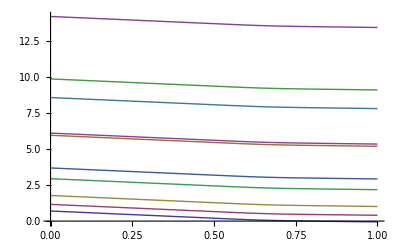

{-1.,1.70011,2.15967,2.77739,3.9441,4.68883,7.11025,6.95835,10.8695,9.57705,15.2072}
{-0.95,1.65011,2.10967,2.72739,3.8941,4.63883,7.06025,6.90835,10.8195,9.52705,15.1572}
{-0.9,1.60011,2.05967,2.67739,3.8441,4.58883,7.01025,6.85835,10.7695,9.47705,15.1072}
{-0.85,1.55011,2.00967,2.62739,3.7941,4.53883,6.96025,6.80835,10.7195,9.42705,15.0572}
{-0.8,1.50011,1.95967,2.57739,3.7441,4.48883,6.91025,6.75835,10.6695,9.37705,15.0072}
{-0.75,1.45011,1.90967,2.52739,3.6941,4.43883,6.86025,6.70835,10.6195,9.32705,14.9572}
{-0.7,1.40011,1.85967,2.47739,3.6441,4.38883,6.81025,6.65835,10.5695,9.27705,14.9072}
{-0.65,1.35011,1.80967,2.42739,3.5941,4.33883,6.76025,6.60835,10.5195,9.22705,14.8572}
{-0.6,1.30011,1.75967,2.37739,3.5441,4.28883,6.71025,6.55835,10.4695,9.17705,14.8072}
{-0.55,1.25011,1.70967,2.32739,3.4941,4.23883,6.66025,6.50835,10.4195,9.12705,14.7572}
{-0.5,1.20011,1.65967,2.27739,3.4441,4.18883,6.61025,6.45835,10.3695,9.07705,14.7072}
{-0.45,1.15011,1.60967,2.22739,3.3941,4.13883,6.56025,6.40835,10.3195,9.02705,14.6572}
{-0.4,1.10011,1.55967,2.17739,3.3441,4.08883,6.51025,6.35835,10.2695,8.97705,14.6072}
{-0.35,1.05011,1.50967,2.12739,3.2941,4.03883,6.46025,6.30835,10.2195,8.92705,14.5572}
{-0.3,1.00011,1.45967,2.07739,3.2441,3.98883,6.41025,6.25835,10.1695,8.87705,14.5072}
{-0.25,0.950109,1.40967,2.02739,3.1941,3.93883,6.36025,6.20835,10.1195,8.82705,14.4572}
{-0.2,0.900109,1.35967,1.97739,3.1441,3.88883,6.31025,6.15835,10.0695,8.77705,14.4072}
{-0.15,0.850109,1.30967,1.92739,3.0941,3.83883,6.26025,6.10835,10.0195,8.72705,14.3572}
{-0.1,0.800109,1.25967,1.87739,3.0441,3.78883,6.21025,6.05835,9.96953,8.67705,14.3072}
{-0.05,0.750109,1.20967,1.82739,2.9941,3.73883,6.16025,6.00835,9.91953,8.62705,14.2572}
{0.,0.700109,1.15967,1.77739,2.9441,3.68883,6.11025,5.95835,9.86953,8.57705,14.2072}
{0.05,0.650109,1.10967,1.72739,2.8941,3.63883,6.06025,5.90835,9.81953,8.52705,14.1572}
{0.1,0.600109,1.05967,1.67739,2.8441,3.58883,6.01025,5.85835,9.76953,8.47705,14.1072}
{0.15,0.550109,1.00967,1.62739,2.7941,3.53883,5.96025,5.80835,9.71953,8.42705,14.0572}
{0.2,0.500109,0.959674,1.57739,2.7441,3.48883,5.91025,5.75835,9.66953,8.37705,14.0072}
{0.25,0.450109,0.909674,1.52739,2.6941,3.43883,5.86025,5.70835,9.61953,8.32705,13.9572}
{0.3,0.400109,0.859674,1.47739,2.6441,3.38883,5.81025,5.65835,9.56953,8.27705,13.9072}
{0.35,0.350109,0.809674,1.42739,2.5941,3.33883,5.76025,5.60835,9.51953,8.22705,13.8572}
{0.4,0.30011,0.759675,1.37739,2.5441,3.28883,5.71025,5.55835,9.46953,8.17705,13.8072}
{0.45,0.250119,0.709684,1.3274,2.49411,3.23884,5.66026,5.50836,9.41954,8.12706,13.7572}
{0.5,0.200178,0.659743,1.27746,2.44417,3.1889,5.61032,5.45842,9.3696,8.07712,13.7073}
{0.55,0.150579,0.610144,1.22784,2.39456,3.13929,5.56071,5.40881,9.31999,8.0275,13.6576}
{0.6,0.103036,0.562601,1.18021,2.34693,3.09167,5.51309,5.36118,9.27236,7.97985,13.61}
{0.65,0.0631693,0.522734,1.13999,2.3067,3.05152,5.47294,5.32095,9.23213,7.93954,13.5697}
{0.7,0.0350118,0.494577,1.11106,2.27777,3.02273,5.44415,5.29202,9.2032,7.91042,13.5406}
{0.75,0.0148949,0.47446,1.08988,2.2566,3.00176,5.42318,5.27085,9.18203,7.88898,13.5191}
{0.8,-0.00121895,0.458346,1.07257,2.23928,2.98467,5.40609,5.25353,9.16471,7.87138,13.5015}
{0.85,-0.0154064,0.444159,1.05711,2.22383,2.96946,5.39088,5.23808,9.14926,7.85561,13.4858}
{0.9,-0.0287266,0.430838,1.04249,2.20921,2.95509,5.37651,5.22346,9.13464,7.84067,13.4708}
{0.95,-0.0420063,0.417559,1.02792,2.19463,2.94075,5.36217,5.20888,9.12006,7.82578,13.4559}
{1.,-0.0559289,0.403636,1.01272,2.17943,2.9258,5.34722,5.19368,9.10486,7.81026,13.4404}

```mathematica
Eq01H[vgs_,vds_,r_,tox_,st_]:=-ws+(subbandtable[[1,3]]+(subbandtable[[1,5]] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]
Eq01L[vgs_,vds_,r_,tox_,st_]:=-ws+(subbandtable[[2,3]]+(subbandtable[[2,5]] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]
Eq11H[vgs_,vds_,r_,tox_,st_]:=-ws+(subbandtable[[3,3]]+(subbandtable[[3,5]] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]
Eq11L[vgs_,vds_,r_,tox_,st_]:=-ws+(subbandtable[[4,3]]+(subbandtable[[4,5]] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]
Eq02H[vgs_,vds_,r_,tox_,subta_]:=-ws+(subbandtable[[5,3]]+(subbandtable[[5,5]] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]
Eq02L[vgs_,vds_,r_,tox_,subta_]:=-ws+(subbandtable[[6,3]]+(subbandtable[[6,5]] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]
Eq12H[vgs_,vds_,r_,tox_,subta_]:=-ws+(subbandtable[[7,3]]+(subbandtable[[7,5]] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]
Eq12L[vgs_,vds_,r_,tox_,subta_]:=-ws+(subbandtable[[8,3]]+(subbandtable[[8,5]] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]
Eq22H[vgs_,vds_,r_,tox_,subta_]:=-ws+(subbandtable[[9,3]]+(subbandtable[[9,5]] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]
Eq22L[vgs_,vds_,r_,tox_,subta_]:=-ws+(subbandtable[[10,3]]+(subbandtable[[10,5]] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]))/.ws->vgs-wgc+wfb-(4 Pi ϵsi)/Cox[R,Tox] multieachsubbandsnumugamyrich[vgs,vds,R,Tox,subbandtable,5]
Plot[{Eq01H[vgs,0.8,R,Tox,subbandtable],Eq01L[vgs,0.8,R,Tox,subbandtable],Eq11H[vgs,0.8,R,Tox,subbandtable],Eq11L[vgs,0.8,R,Tox,subbandtable],Eq02H[vgs,0.8,R,Tox,subbandtable],Eq02L[vgs,0.8,R,Tox,subbandtable],Eq12H[vgs,0.8,R,Tox,subbandtable],Eq12L[vgs,0.8,R,Tox,subbandtable],Eq22H[vgs,0.8,R,Tox,subbandtable],Eq22L[vgs,0.8,R,Tox,subbandtable]},{vgs,0,1}]
Column[Table[{vgs,Eq01H[vgs,0.8,R,Tox,subbandtable],Eq01L[vgs,0.8,R,Tox,subbandtable],Eq11H[vgs,0.8,R,Tox,subbandtable],Eq11L[vgs,0.8,R,Tox,subbandtable],Eq02H[vgs,0.8,R,Tox,subbandtable],Eq02L[vgs,0.8,R,Tox,subbandtable],Eq12H[vgs,0.8,R,Tox,subbandtable],Eq12L[vgs,0.8,R,Tox,subbandtable],Eq22H[vgs,0.8,R,Tox,subbandtable],Eq22L[vgs,0.8,R,Tox,subbandtable]},{vgs,-1,1,0.05}]]
```

```mathematica
VDS=0.8
```

0.8

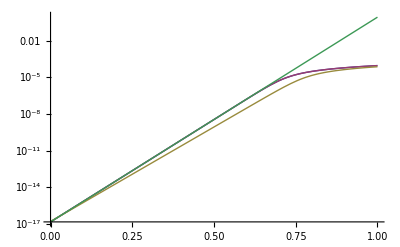

```mathematica
LogPlot[{(e kB T)/(Pi hbar) subbandtable[[1,1]] (Log[1+Exp[1/vt(vgs-wgc+wfb)-subbandtable[[1,4]]]]-Log[1+Exp[1/vt(vgs-wgc+wfb)-subbandtable[[1,4]]-VDS/vt]]),(e kB T)/(Pi hbar) subbandtable[[1,1]] (Log[1+Exp[1/vt(vgs-wgc+wfb)-subbandtable[[1,4]]]]),(e kB T1)/(Pi hbar) subbandtable[[1,1]] (Log[1+Exp[1/vt1(vgs-wgc+wfb)-subbandtable[[1,4]]]]-Log[1+Exp[1/vt1(vgs-wgc+wfb)-subbandtable[[1,4]]-VDS/vt1]]),(e kB T)/(Pi hbar) subbandtable[[1,1]] (Exp[1/vt(vgs-wgc+wfb)-subbandtable[[1,4]]]-Exp[1/vt(vgs-wgc+wfb)-subbandtable[[1,4]]-VDS/vt])},{vgs,0,1}]
```

```mathematica
1/vt(VGS0-wgc+wfb)-subbandtable[[1,4]]
```

-27.0812+38.6815 (0.+VGS0)

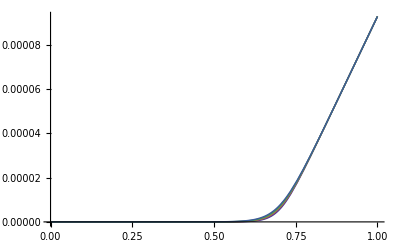

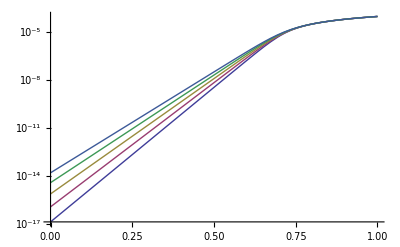

E:\data_for_mathematica\thmeralcurrent.txt

```mathematica
Plot[{(e kB T)/(Pi hbar) subbandtable[[1,1]] (Log[1+Exp[1/vt(vgs-wgc+wfb)-besselenergylevel[0,1,mr,R]/(kB T)]]),(e kB T1)/(Pi hbar) subbandtable[[1,1]] (Log[1+Exp[1/vt1(vgs-wgc+wfb)-besselenergylevel[0,1,mr,R]/(kB T1)]]),(e kB T2)/(Pi hbar) subbandtable[[1,1]] (Log[1+Exp[1/vt2(vgs-wgc+wfb)-besselenergylevel[0,1,mr,R]/(kB T2)]]),(e kB T3)/(Pi hbar) subbandtable[[1,1]] (Log[1+Exp[1/vt3(vgs-wgc+wfb)-besselenergylevel[0,1,mr,R]/(kB T3)]]),(e kB T4)/(Pi hbar) subbandtable[[1,1]] (Log[1+Exp[1/vt4(vgs-wgc+wfb)-besselenergylevel[0,1,mr,R]/(kB T4)]])},{vgs,0,1}]
LogPlot[{(e kB T)/(Pi hbar) subbandtable[[1,1]] (Log[1+Exp[1/vt(vgs-wgc+wfb)-besselenergylevel[0,1,mr,R]/(kB T)]]),(e kB T1)/(Pi hbar) subbandtable[[1,1]] (Log[1+Exp[1/vt1(vgs-wgc+wfb)-besselenergylevel[0,1,mr,R]/(kB T1)]]),(e kB T2)/(Pi hbar) subbandtable[[1,1]] (Log[1+Exp[1/vt2(vgs-wgc+wfb)-besselenergylevel[0,1,mr,R]/(kB T2)]]),(e kB T3)/(Pi hbar) subbandtable[[1,1]] (Log[1+Exp[1/vt3(vgs-wgc+wfb)-besselenergylevel[0,1,mr,R]/(kB T3)]]),(e kB T4)/(Pi hbar) subbandtable[[1,1]] (Log[1+Exp[1/vt4(vgs-wgc+wfb)-besselenergylevel[0,1,mr,R]/(kB T4)]])},{vgs,0,1}]
Export["E:\data_for_mathematica\\thmeralcurrent.txt",Table[{vgs,(e kB T)/(Pi hbar) subbandtable[[1,1]] (Log[1+Exp[1/vt(vgs-wgc+wfb)-besselenergylevel[0,1,mr,R]/(kB T)]]),(e kB T1)/(Pi hbar) subbandtable[[1,1]] (Log[1+Exp[1/vt1(vgs-wgc+wfb)-besselenergylevel[0,1,mr,R]/(kB T1)]]),(e kB T2)/(Pi hbar) subbandtable[[1,1]] (Log[1+Exp[1/vt2(vgs-wgc+wfb)-besselenergylevel[0,1,mr,R]/(kB T2)]]),(e kB T3)/(Pi hbar) subbandtable[[1,1]] (Log[1+Exp[1/vt3(vgs-wgc+wfb)-besselenergylevel[0,1,mr,R]/(kB T3)]]),(e kB T4)/(Pi hbar) subbandtable[[1,1]] (Log[1+Exp[1/vt4(vgs-wgc+wfb)-besselenergylevel[0,1,mr,R]/(kB T4)]])},{vgs,-1,2,0.01}],"CSV"]
```